```mathematica
A[n_]:=SeriesCoefficient[Sqrt[y*t^3-x*t^2+t-1],{t,0,n}]
```

```mathematica
Factor[Det[HankelMatrix[{A[2]},{A[2]}]]]
```

1/8 ⅈ (-1+4 x)

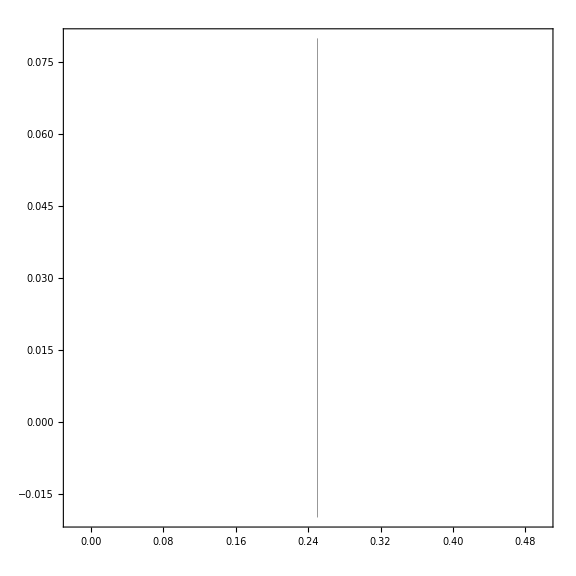

```mathematica
ContourPlot[-1+4 x==0,{x,-0.02,0.5},{y,-0.02,0.08},PerformanceGoal->"Quality",PlotPoints->1000,MaxRecursion->2,ImageSize->Large,AspectRatio->1,Frame->{{True,False},{True,False}},Axes->False,ContourStyle->Thickness[0.0005]]
```

```mathematica
Export["Desktop/triangles.png",Graphics[%],Background->None,ImageResolution->500]
```

Desktop/triangles.png

```mathematica
Factor[Det[HankelMatrix[{A[3]},{A[3]}]]]
```

1/16 ⅈ (-1+4 x-8 y)

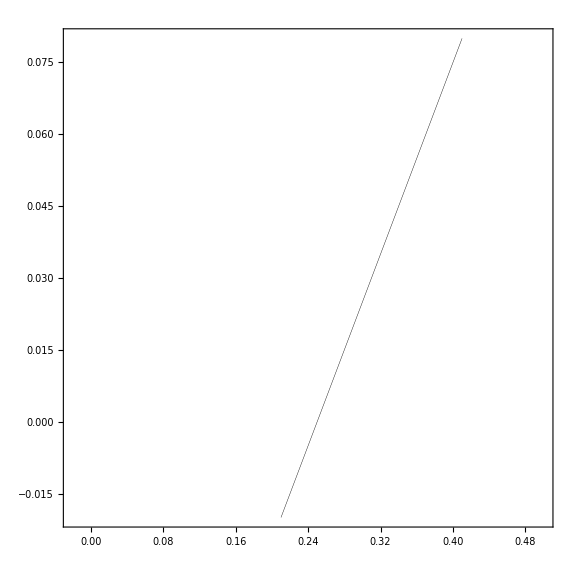

```mathematica
ContourPlot[-1+4 x-8 y==0,{x,-0.02,0.5},{y,-0.02,0.08},PerformanceGoal->"Quality",PlotPoints->1000,MaxRecursion->2,ImageSize->Large,AspectRatio->1,Frame->{{True,False},{True,False}},Axes->False,ContourStyle->Thickness[0.0005]]
```

```mathematica
Export["Desktop/quadrilaterals.png",Graphics[%],Background->None,ImageResolution->500]
```

Desktop/quadrilaterals.png

```mathematica
Factor[Det[HankelMatrix[{A[2],A[3]},{A[3],A[4]}]]]
```

(-1+12 x-48 x^2+64 x^3+32 y-128 x y+256 y^2)/1024

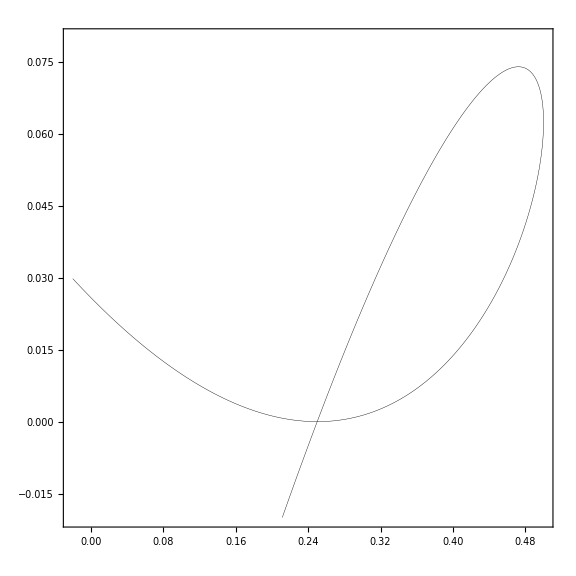

```mathematica
ContourPlot[-1+12 x-48 x^2+64 x^3+32 y-128 x y+256 y^2==0,{x,-0.02,0.5},{y,-0.02,0.08},PerformanceGoal->"Quality",PlotPoints->1000,MaxRecursion->2,ImageSize->Large,AspectRatio->1,Frame->{{True,False},{True,False}},Axes->False,ContourStyle->Thickness[0.0005]]
```

```mathematica
Export["Desktop/pentagons.png",Graphics[%],Background->None,ImageResolution->500]
```

Desktop/pentagons.png

```mathematica
Factor[Det[HankelMatrix[{A[3],A[4]},{A[4],A[5]}]]]
```

((-1+4 x) (3-20 x+16 x^2+64 x^3+96 y-384 x y+512 y^2))/16384

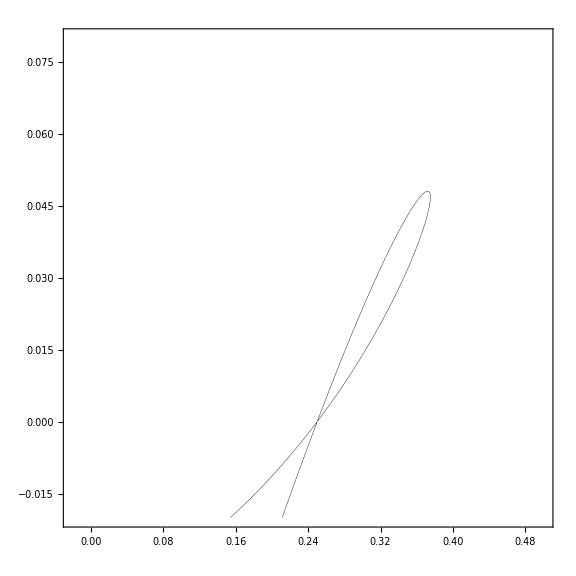

```mathematica
ContourPlot[3-20 x+16 x^2+64 x^3+96 y-384 x y+512 y^2==0,{x,-0.02,0.5},{y,-0.02,0.08},PerformanceGoal->"Quality",PlotPoints->1000,MaxRecursion->2,ImageSize->Large,AspectRatio->1,Frame->{{True,False},{True,False}},Axes->False,ContourStyle->Thickness[0.0005]]
```

```mathematica
Export["Desktop/hexagons.png",Graphics[%],Background->None,ImageResolution->500]
```

Desktop/hexagons.png

```mathematica
Factor[Det[HankelMatrix[{A[2],A[3],A[4]},{A[4],A[5],A[6]}]]]
```

(ⅈ (1-24 x+240 x^2-1280 x^3+3840 x^4-6144 x^5+4096 x^6-160 y+2048 x y-9216 x^2 y+16384 x^3 y-8192 x^4 y-3328 y^2+27648 x y^2-61440 x^2 y^2+16384 x^3 y^2-24576 y^3+98304 x y^3-65536 y^4))/2097152

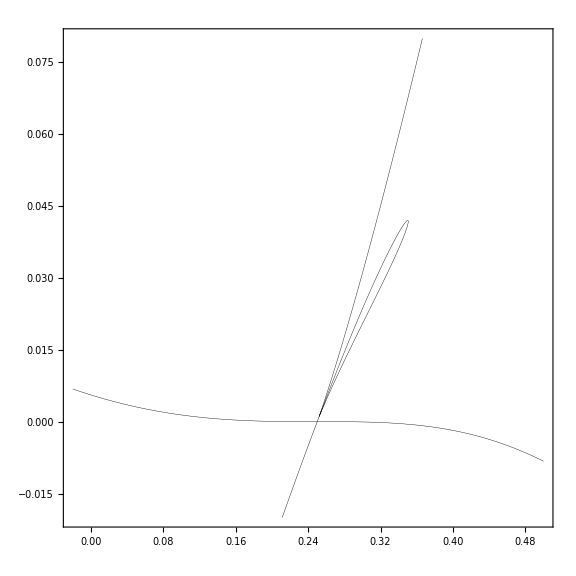

```mathematica
ContourPlot[1-24 x+240 x^2-1280 x^3+3840 x^4-6144 x^5+4096 x^6-160 y+2048 x y-9216 x^2 y+16384 x^3 y-8192 x^4 y-3328 y^2+27648 x y^2-61440 x^2 y^2+16384 x^3 y^2-24576 y^3+98304 x y^3-65536 y^4==0,{x,-0.02,0.5},{y,-0.02,0.08},PerformanceGoal->"Quality",PlotPoints->1000,MaxRecursion->2,ImageSize->Large,AspectRatio->1,Frame->{{True,False},{True,False}},Axes->False,ContourStyle->Thickness[0.0005]]
```

```mathematica
Export["Desktop/septagons.png",Graphics[%],Background->None,ImageResolution->500]
```

Desktop/septagons.png